```mathematica
Get["genic-selection_1.m"];

For[k = 0, k ≤4,k++,
Josh[k] = Exp[γ  (y  - x)]* Sum[(-1/2)^j (γ)^(2j) * o[j], {j, 0, k}]
]
Clear[o]
```

```mathematica
Kimura[x_,y_,t_,n_]:= Module[{m},Sum[4*(2*m+1)*x*(1-x)/(m*(m+1))*GegenbauerC[m-1,3/2,1-2*x]*GegenbauerC[m-1,3/2,1-2*y]*Exp[-1/2*m*(m+1)*t],{m,1,n}]
]
neutral = Kimura[x,y,t,50];
```

```mathematica
Get["path-integrals.m"];
haywardVGMinus4 = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pints[[j]][[1]],{j,1,4}]);
haywardVGMinus3 = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pints[[j]][[2]],{j,1,4}]);
haywardVGMinus2 = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pints[[j]][[3]],{j,1,4}]);
haywardVGMinus1 = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* (Kimura[x,y,t,50] + Sum[(2 Ne^2 α Λ / W^2)^j pints[[j]][[4]],{j,1,4}]);
```

```mathematica
Clear[pints];
```

```mathematica
Clear[fitVar, selectedNe, jumpSize, selCoef, genVar, start,time, soln];
fitVar = 1;
selectedNe = 500;
jumpSize = 1;
start = 0.2;
time = 0.25;
selCoef =.005;
```

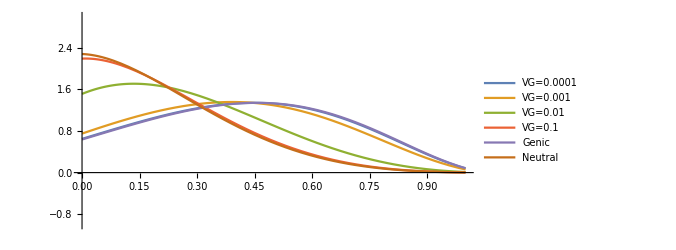

```mathematica
Plot[{Evaluate[haywardVGMinus4/.{x->start,t->time,α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> 0.0001, W->fitVar}],
Evaluate[haywardVGMinus3/.{x->start,t->time,α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> 0.001, W->fitVar}],
Evaluate[haywardVGMinus2/.{x->start,t->time,α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> 0.01, W->fitVar}],
Evaluate[haywardVGMinus1/.{x->start,t->time,α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> 0.1, W->fitVar}],
Evaluate[Josh[4]/.{x->start,t->time,γ->5}],
Evaluate[neutral /. {x->start,t->time}]},
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2,
PlotLegends->{TextString@Row@{"VG=",0.0001},
TextString@Row@{"VG=",0.001},
TextString@Row@{"VG=",0.01},
TextString@Row@{"VG=",0.1},
"Genic",
"Neutral"},
PlotRange->{{0,1},{-1,3}}]
```

```mathematica
Do[Clear[minus4, minus3, minus2, minus1, genic, neutr];
Print[i];
minus4 = Evaluate[haywardVGMinus4/.{x->start,t->time,α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> 0.0001, W->fitVar, y ->i}];
minus3 = Evaluate[haywardVGMinus3/.{x->start,t->time,α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> 0.001, W->fitVar, y ->i}];
minus2 =Evaluate[haywardVGMinus2/.{x->start,t->time,α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> 0.01, W->fitVar, y ->i}];
minus1 =Evaluate[haywardVGMinus1/.{x->start,t->time,α->selCoef,Λ->jumpSize, Ne -> selectedNe, VG -> 0.1, W->fitVar, y ->i}];
genic = Evaluate[Josh[4]/.{x->start,t->time,γ->5, y ->i}];
neutr  = Evaluate[neutral /. {x->start,t->time, y ->i}];
Export[StringJoin["comparison_",ToString[i],".csv"], {minus4, minus3, minus2, minus1, genic, neutr},"csv"],
{i, 0, 1, 0.01}]
```

0.

0.01

0.02

0.03

0.04

0.05

0.06

0.07

0.08

0.09

0.1

0.11

0.12

0.13

0.14

0.15

0.16

0.17

0.18

0.19

0.2

0.21

0.22

0.23

0.24

0.25

0.26

0.27

0.28

0.29

0.3

0.31

0.32

0.33

0.34

0.35

0.36

0.37

0.38

0.39

0.4

0.41

0.42

0.43

0.44

0.45

0.46

0.47

0.48

0.49

0.5

0.51

0.52

0.53

0.54

0.55

0.56

0.57

0.58

0.59

0.6

0.61

0.62

0.63

0.64

0.65

0.66

0.67

0.68

0.69

0.7

0.71

0.72

0.73

0.74

0.75

0.76

0.77

0.78

0.79

0.8

0.81

0.82

0.83

0.84

0.85

0.86

0.87

0.88

0.89

0.9

0.91

0.92

0.93

0.94

0.95

0.96

0.97

0.98

0.99

1.